```mathematica
Clear["Global`*"]
```

```mathematica
g = 9.81;
l = 1;
Ω = 30;
A = 0.2;
α=g/l*1/Ω^2;
β = -A/l;
ω0=Sqrt[g/l];
A/l * Ω/ω0
eqs={x'[t]==y[t],y'[t]== (α+β*Cos[t])*x[t]};
ics10={x[0]==1,y[0]==0};
ics01={x[0]==0,y[0]==1};
vars={x[t],y[t]};
T =2*Pi;
time={t,0,T};
(*period T vychazi z cos t* tedy... T*=omega T.... T = 2 Pi/omega *)
```

1.91565

```mathematica
sol1 = NDSolve[{eqs,ics10},vars,time];
sol2 = NDSolve[{eqs,ics01},vars,time];
vek1 = Splice[vars] /.sol1/.t->T;
vek2 =  Splice[vars] /.sol2 /.t->T;
```

Matrix of monodromy (t0=0)

```mathematica
Ε=Transpose[{vek1,vek2}] ;
Ε//MatrixForm
Det[Ε]
Tr[Ε]
vlcis = Eigenvalues[Ε]
vlcis[[1]]*vlcis[[2]]
```

(0.818294 | 9.17918
-0.0359939 | 0.818295)

1.

1.63659

{0.818295+0.574799 ⅈ,0.818295-0.574799 ⅈ}

1.+0. ⅈ

Ověření

```mathematica
sol=NDSolve[{θ''[t] +(g/l-(A Ω^2/l) Cos[Ω t])Sin[θ[t]]==0, θ[0]==Pi+0.1, θ'[0] == 0}, θ[t], {t,0, 100*π*Sqrt[l/g] }];
Animate[Graphics[{EdgeForm[Thick],White,Rectangle[{-1.65,-1.65},{1.65,1.65}],Black,Disk[{0,A Cos[Ω s]},0.01],Line[{{0,A Cos[Ω s]},{l Sin[θ[t]]/.sol[[1]]/.t->s,A Cos[Ω s]- l Cos[θ[t]]/.sol[[1]]/.t->s}}],Disk[{l Sin[θ[t]]/.sol[[1]]/.t->s,A Cos[Ω s]- l Cos[θ[t]]/.sol[[1]]/.t->s},0.02]}],{s,0, 20*π*Sqrt[l/g],20*π*Sqrt[l/g]/10000},AnimationRate->0.5]
```

Global picture

```mathematica
Stability[α_, β_]:=(
sol1 = NDSolve[{x'[t]==y[t],y'[t]== -(α+β*Cos[t])*x[t],x[0]==1,y[0]==0},{x[t],y[t]},{t,0,T}];
sol2 = NDSolve[{x'[t]==y[t],y'[t]== -(α+β*Cos[t])*x[t],x[0]==0,y[0]==1},{x[t],y[t]},{t,0,T}];
vek1 = Splice[vars] /.sol1/.t->T;
vek2 =  Splice[vars] /.sol2 /.t->T;
Ε=Transpose[{vek1,vek2}] ;
Boole[-2≤ Tr[Ε]≤ 2]
)
```

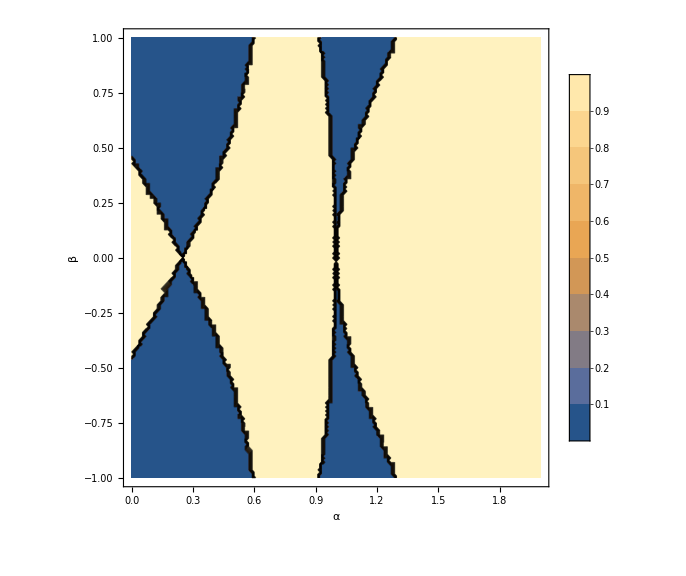

```mathematica
ContourPlot[Stability[α,β],{α,0,2},{β ,-1,1},PlotLegends->Automatic,FrameLabel->{"α","β"},AspectRatio->1,ImageSize->Large]
```

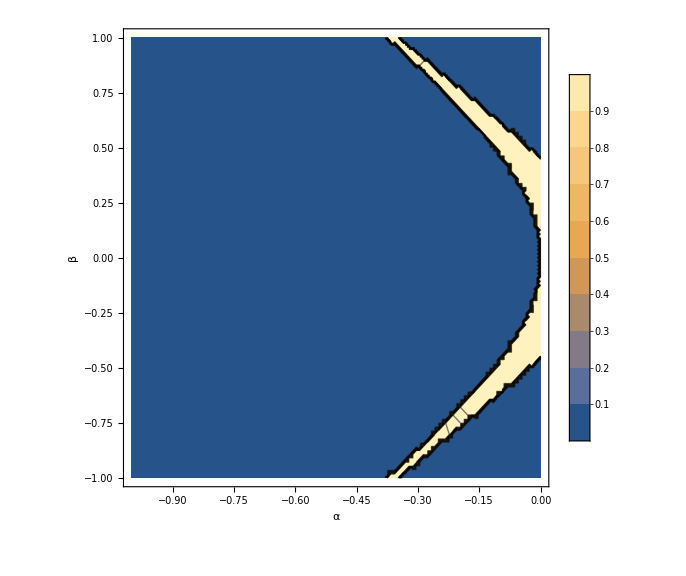

```mathematica
ContourPlot[Stability[α,β],{α,-1,0},{β ,-1,1},PlotLegends->Automatic,FrameLabel->{"α","β"},AspectRatio->1,ImageSize->Large]
```

POROVNANI S BRUTE FORCE

```mathematica
Stability2[Ωω_, Al_]:=(
sol1 = NDSolve[{x'[t]==y[t],y'[t]== (1/Ωω^2- Al*Cos[t])*x[t],x[0]==1,y[0]==0},{x[t],y[t]},{t,0,T}];
sol2 = NDSolve[{x'[t]==y[t],y'[t]== (1/Ωω^2- Al*Cos[t])*x[t],x[0]==0,y[0]==1},{x[t],y[t]},{t,0,T}];
vek1 = Splice[vars] /.sol1/.t->T;
vek2 =  Splice[vars] /.sol2 /.t->T;
Ε=Transpose[{vek1,vek2}] ;
Boole[-2≤ Tr[Ε]≤ 2]
)
```

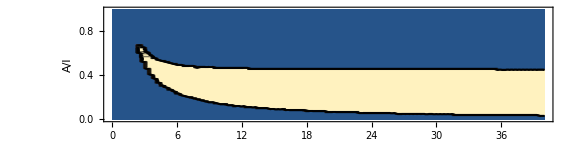

```mathematica
ContourPlot[Stability2[Ωω,Al],{Ωω,0,40},{Al,0,1},PlotLegends->Automatic,FrameLabel->{"Ω/ω_0","A/l"},AspectRatio->0.25,ImageSize->Large]
```